## H(t)

```mathematica
Ht[Nl_, centre_, A_, ω_, t_, ϕ_]:= Table[If[Abs[i-j]==1, -1, If[i==j &&i == centre, A*Cos[ω*t + ϕ], 0]], {i, 1, Nl}, {j, 1, Nl}]
Ht[7, 4, A, ω, t, ϕ] // MatrixForm
```

(0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0 | -1 | 0 | 0 | 0
0 | 0 | -1 | A Cos[ϕ+t ω] | -1 | 0 | 0
0 | 0 | 0 | -1 | 0 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0)

#### Density Evolution

```mathematica
ClearAll@ψ1;
ClearAll@ψ2;

(*conditions*)
 Nlat = 71; (*size of lattice*)
sitestart = 35; (*position atom starts*)

AA = 35;  ωω=9.6; ϕϕ1 = Pi/3; ϕϕ2 = Pi/7; (*time dependent potential parameters*)
T = 2π/ωω;
centre = 25; (*site of oscillation*)

Noscillations = 15;
Ntimesteps = 10*Noscillations;
tf = T*Noscillations;
tstep = tf/ Ntimesteps; 

(* Solve wavefunction for two different phi*)
ψ0 = Table[If[i==sitestart,1,0],{i,1,Nlat}];
s1=NDSolve[{-I *D[ψ1[t], t]== Ht[Nlat, centre, AA, ωω, t, ϕϕ1].ψ1[t], ψ1[0] == ψ0}, ψ1, {t, 0, tf}];
ψ1[t_]=Evaluate[ψ1[t]/.s1]; 
s2=NDSolve[{-I* D[ψ2[t], t]== Ht[Nlat, centre, AA, ωω, t, ϕϕ2].ψ2[t], ψ2[0]== ψ0}, ψ2, {t, 0, tf}];
ψ2[t_]=Evaluate[ψ2[t]/.s2];
```

```mathematica
(*set x ticks to have units of the oscillation period T*)
xrow=Table[If[Divisible[i, Round[Ntimesteps/Noscillations]]==True,i/Round[Ntimesteps/Noscillations],""],{i,0,Ntimesteps}];
xticksMatrix=MapIndexed[{#2[[1]],#}&,xrow];
(*ycolumn=Table[ If[Divisible[i, 10]==True,i,""],{i,0,10*2}];
yticksMatrix=MapIndexed[{#2[[1]],#}&,ycolumn];*)
```

A = 35, ω = 9.6, ϕ = π/3

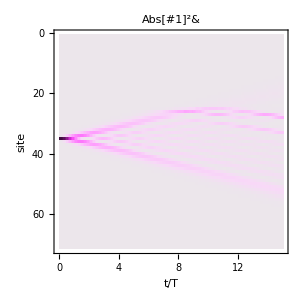
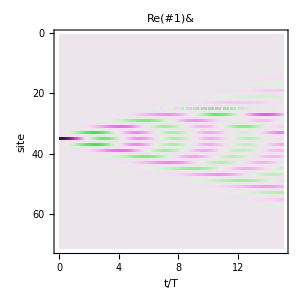
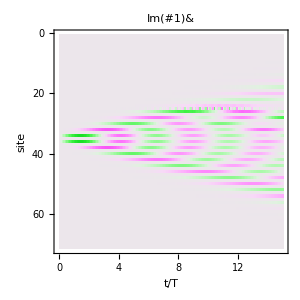

A = 35, ω = 9.6, ϕ = π/7

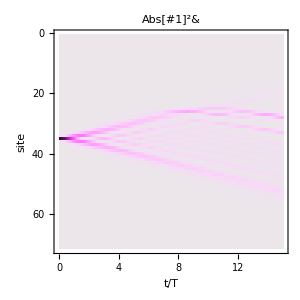
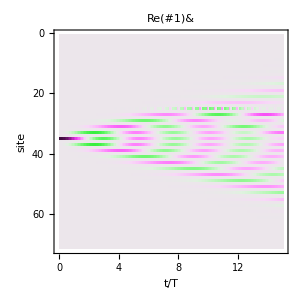
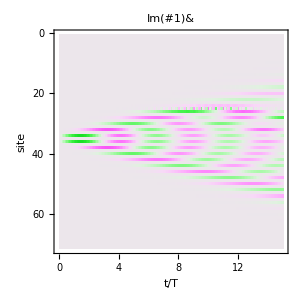

```mathematica
(*Graph Ntimesteps / Noscillations steps per period: *)
Print["A = ", AA, ", ω = ", ωω, ", ϕ = ", ϕϕ1]
Append[Table[MatrixPlot[Table[f[ψ1[t][[1, i]]], {i, 1, Nlat}, {t, 0, tf, tstep}], FrameLabel->{"site","t/T"},   FrameTicks->{{{0, 10, 20, 30, 40, 50, 60, 70},None},{xticksMatrix,xticksMatrix}}, ImageSize-> {300,300}, ColorFunction->ColorData[{"GreenPinkTones", {-1, 1}}], ColorFunctionScaling->False, PlotLabel -> f], {f,{Abs[#]^2&,Re[#]&, Im[#]&}}], BarLegend[{"GreenPinkTones", {-1, 1}}]]
Print["A = ", AA, ", ω = ", ωω, ", ϕ = ", ϕϕ2]
Append[Table[MatrixPlot[Table[f[ψ2[t][[1, i]]], {i, 1, Nlat}, {t, 0, tf, tstep}], FrameLabel->{"site","t/T"},   FrameTicks->{{{0, 10, 20, 30, 40, 50, 60, 70},None},{xticksMatrix,xticksMatrix}}, ImageSize-> {300,300}, ColorFunction->ColorData[{"GreenPinkTones", {-1, 1}}], ColorFunctionScaling->False, PlotLabel -> f], {f,{Abs[#]^2&,Re[#]&, Im[#]&}}], BarLegend[{"GreenPinkTones", {-1, 1}}]]
```

#### Difference between wavefunctions at different ϕ

```mathematica
(*Total difference between density plots*)
Diff[f_]:=Mean[Abs[Flatten[Table[f[#1[t][[1,i]]]-f[#2[t][[1,i]]], {i, #3, #4},{t, #5, tf, #6}]]]]&;

Grid[{{"time range",  "site range","tstep", "Abs", "Re", "Imag"},
{ "0->15T",  "1->Nlat","T/10", Diff[Abs][ ψ1, ψ2, 1, Nlat, 0, tstep], Diff[Re][ ψ1, ψ2,  1, Nlat, 0, tstep],Diff[Im][ ψ1, ψ2,   1, Nlat, 0, tstep]},
{ "0->15T","1->Nlat", "T", Diff[Abs][ ψ1, ψ2, 1, Nlat, 0, T], Diff[Re][ ψ1, ψ2,  1, Nlat, 0, T],Diff[Im][ ψ1, ψ2,   1, Nlat, 0, T]},
{ "0->15T", "25","T/10",Diff[Abs][ ψ1, ψ2, 25, 25, 0, tstep],Diff[Re][ ψ1, ψ2, 25, 25, 0, tstep],Diff[Im][ ψ1, ψ2, 25, 25, 0, tstep]},
{ "0->15T", "25","T", Diff[Abs][ ψ1, ψ2, 25, 25, 0, T],Diff[Re][ ψ1, ψ2, 25, 25, 0, T],Diff[Im][ ψ1, ψ2, 25, 25, 0, T]},
{ "8T->15T", "25","T/10",Diff[Abs][ ψ1, ψ2, 25, 25, 8*T, tstep],Diff[Re][ ψ1, ψ2, 25, 25, 8*T, tstep],Diff[Im][ ψ1, ψ2, 25, 25, 8*T, tstep]},
{ "8T->15T", "25","T", Diff[Abs][ ψ1, ψ2, 25, 25, 8*T, T],Diff[Re][ ψ1, ψ2, 25, 25, 8*T, T],Diff[Im][ ψ1, ψ2, 25, 25, 8*T, T]},
{ "8T->15T","24","T/10", Diff[Abs][ ψ1, ψ2, 24, 24, 8*T, tstep],Diff[Re][ ψ1, ψ2, 24, 24, 8*T, tstep],Diff[Im][ ψ1, ψ2, 24, 24, 8*T, tstep]},
{"8T->15T",  "24","T", Diff[Abs][ ψ1, ψ2, 24, 24, 8*T, T],Diff[Re][ ψ1, ψ2, 24, 24, 8*T, T],Diff[Im][ ψ1, ψ2, 24, 24, 8*T, T]},
{ "8T->15T","23","T/10", Diff[Abs][ ψ1, ψ2, 23, 23, 8*T, tstep],Diff[Re][ ψ1, ψ2, 23, 23, 8*T, tstep],Diff[Im][ ψ1, ψ2, 23, 23, 8*T, tstep]},
{"8T->15T", "23","T", Diff[Abs][ ψ1, ψ2, 23, 23, 8*T, T],Diff[Re][ ψ1, ψ2, 23, 23, 8*T, T],Diff[Im][ ψ1, ψ2, 23, 23, 8*T, T]},
{ "8T->15T","22","T/10", Diff[Abs][ ψ1, ψ2, 22, 22, 8*T, tstep],Diff[Re][ ψ1, ψ2, 22, 22, 8*T, tstep],Diff[Im][ ψ1, ψ2, 22, 22, 8*T, tstep]},
{"8T->15T", "22","T", Diff[Abs][ ψ1, ψ2, 22, 22, 8*T, T],Diff[Re][ ψ1, ψ2, 22, 22, 8*T, T],Diff[Im][ ψ1, ψ2, 22, 22, 8*T, T]}}]
```

time range | site range | tstep | Abs | Re | Imag
0->15T | 1->Nlat | T/10 | 0.000189097 | 0.00110662 | 0.0013151
0->15T | 1->Nlat | T | 0.00010386 | 0.00149579 | 0.00148927
0->15T | 25 | T/10 | 0.00586831 | 0.0723211 | 0.0859336
0->15T | 25 | T | 0.00316341 | 0.0985692 | 0.101982
8T->15T | 25 | T/10 | 0.00932508 | 0.136304 | 0.161658
8T->15T | 25 | T | 0.00502556 | 0.183991 | 0.191227
8T->15T | 24 | T/10 | 0.00673691 | 0.00558059 | 0.00675385
8T->15T | 24 | T | 0.00343872 | 0.00668681 | 0.00344742
8T->15T | 23 | T/10 | 0.000339619 | 0.000339493 | 0.000203922
8T->15T | 23 | T | 0.000508264 | 0.000507928 | 0.0000804418
8T->15T | 22 | T/10 | 0.0000169738 | 0.0000146357 | 0.0000169689
8T->15T | 22 | T | 1.1949×10^-6 | 0.0000201144 | 1.18378×10^-6

```mathematica
(*Max differences*)
MaxDiff[f_]:=Max[Abs[Flatten[Table[f[#1[t][[1,i]]]-f[#2[t][[1,i]]], {i, #3, #4},{t, #5, tf, #6}]]]]&;

Grid[{{"time range", "site range",  "tstep","Abs", "Re", "Imag"},
{ "0-15T",  "1->Nlat","T/10",MaxDiff[Abs][ ψ1, ψ2, 1, Nlat, 0, tstep],MaxDiff[Re][ ψ1, ψ2, 1, Nlat, 0, tstep],MaxDiff[Im][ ψ1, ψ2, 1, Nlat, 0, tstep]},
{  "0-15T", "1->Nlat", "T",MaxDiff[Abs][ ψ1, ψ2, 1, Nlat, 0, T],MaxDiff[Re][ ψ1, ψ2, 1, Nlat, 0, T],MaxDiff[Im][ ψ1, ψ2, 1, Nlat, 0, T]}}]
```

time range | site range | tstep | Abs | Re | Imag
0-15T | 1->Nlat | T/10 | 0.0334057 | 0.545859 | 0.545544
0-15T | 1->Nlat | T | 0.008378 | 0.329442 | 0.339639

## H_effective

```mathematica
expbessel1[A_, ω_, ϕ_]:= Exp[I*A*Sin[ϕ]/ω]*BesselJ[0,A/ω];
expbessel2[A_, ω_, ϕ_]:= Exp[-I*A*Sin[ϕ]/ω]*BesselJ[0,A/ω];
HEff[Nl_, centre_, A_, ω_, ϕ_]:= Table[If[Abs[i-j]==1, If[i==centre, expbessel1[A, ω, ϕ], If[j==centre, expbessel2[A, ω, ϕ], -1]], 0], {i, 1, Nl}, {j, 1, Nl}]; 
HEff[7, 4, A, ω, ϕ] // MatrixForm
```

(0 | -1 | 0 | 0 | 0 | 0 | 0
-1 | 0 | -1 | 0 | 0 | 0 | 0
0 | -1 | 0 | ⅇ^(-(ⅈ A Sin[ϕ])/ω) BesselJ[0,A/ω] | 0 | 0 | 0
0 | 0 | ⅇ^((ⅈ A Sin[ϕ])/ω) BesselJ[0,A/ω] | 0 | ⅇ^((ⅈ A Sin[ϕ])/ω) BesselJ[0,A/ω] | 0 | 0
0 | 0 | 0 | ⅇ^(-(ⅈ A Sin[ϕ])/ω) BesselJ[0,A/ω] | 0 | -1 | 0
0 | 0 | 0 | 0 | -1 | 0 | -1
0 | 0 | 0 | 0 | 0 | -1 | 0)

#### Density Evolution

```mathematica
ClearAll@ψ3;
ClearAll@ψ4;

(*conditions*)
 Nlat = 71; (*size of lattice*)
sitestart = 35; (*position atom starts*)

AA = 35;  ωω=9.6; ϕϕ1 = Pi/3; ϕϕ2 = Pi/7; (*time dependent potential parameters*)
T = 2π/ωω;
centre = 25; (*site of oscillation*)

Noscillations = 15;
Ntimesteps = 10*Noscillations;
tf = T*Noscillations;
tstep = tf/ Ntimesteps; 

(* Solve wavefunction for two different phi*)
ψ0 = Table[If[i==sitestart,1,0],{i,1,Nlat}];
s3=NDSolve[{-I* D[ψ3[t], t]== HEff[Nlat, centre, AA, ωω, ϕϕ1].ψ3[t], ψ3[0] == ψ0}, ψ3, {t, 0, tf}];
ψ3[t_]=Evaluate[ψ3[t]/.s3]; 
s4=NDSolve[{-I* D[ψ4[t], t]== HEff[Nlat, centre, AA, ωω, ϕϕ2].ψ4[t], ψ4[0]== ψ0}, ψ4, {t, 0, tf}];
ψ4[t_]=Evaluate[ψ4[t]/.s4];
```

```mathematica
(*set x ticks to have units of the oscillation period T*)
xrow=Table[If[Divisible[i, Round[Ntimesteps/Noscillations]]==True,i/Round[Ntimesteps/Noscillations],""],{i,0,Ntimesteps}];
xticksMatrix=MapIndexed[{#2[[1]],#}&,xrow];
(*ycolumn=Table[ If[Divisible[i, 10]==True,i,""],{i,0,10*2}];
yticksMatrix=MapIndexed[{#2[[1]],#}&,ycolumn];*)
```

A = 35, ω = 9.6, ϕ = π/3

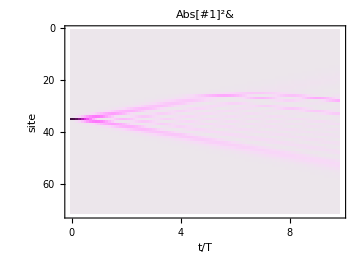
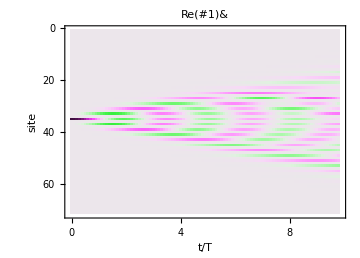
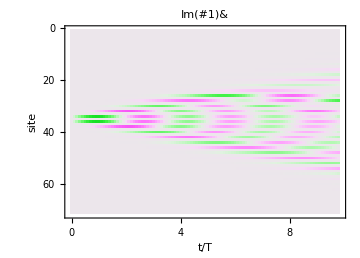

A = 35, ω = 9.6, ϕ = π/7

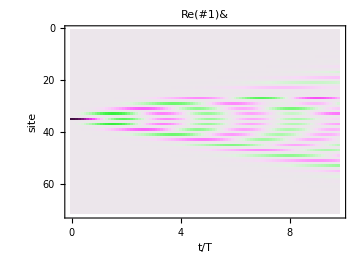
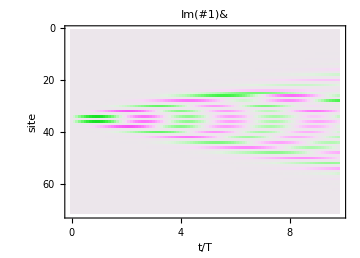
{-Graphics-,-Graphics-,-Graphics-,}

```mathematica
Print["A = ", AA, ", ω = ", ωω, ", ϕ = ", ϕϕ1]
Append[Table[MatrixPlot[Table[f[ψ3[t][[1, i]]], {i, 1, Nlat}, {t, 0, tf, Noscillations/Ntimesteps}], FrameLabel->{"site","t/T"},   FrameTicks->{{{0, 10, 20, 30, 40, 50, 60, 70},None},{xticksMatrix,xticksMatrix}}, ImageSize-> Medium, ColorFunction->ColorData[{"GreenPinkTones", {-1, 1}}], ColorFunctionScaling->False, PlotLabel -> f], {f,{Abs[#]^2&,Re[#]&, Im[#]&}}], BarLegend[{"GreenPinkTones", {-1, 1}}]]
Print["A = ", AA, ", ω = ", ωω, ", ϕ = ", ϕϕ2]
Append[Table[MatrixPlot[Table[f[ψ4[t][[1, i]]], {i, 1, Nlat}, {t, 0, tf, Noscillations/Ntimesteps}], FrameLabel->{"site","t/T"},   FrameTicks->{{{0, 10, 20, 30, 40, 50, 60, 70},None},{xticksMatrix,xticksMatrix}}, ImageSize-> Medium, ColorFunction->ColorData[{"GreenPinkTones", {-1, 1}}], ColorFunctionScaling->False, PlotLabel -> f], {f,{Abs[#]^2&,Re[#]&, Im[#]&}}], BarLegend[{"GreenPinkTones", {-1, 1}}]]
```

#### Difference between wavefunctions at different ϕ

```mathematica
(*Total difference between density plots*)
(*More granular calculation including micromotion*)

Grid[{{  "time range","site range","tstep", "Abs", "Re", "Imag"},
{ "0->15T", "1->Nlat","T",Diff[Abs][ ψ3, ψ4, 1, Nlat, 0, T], Diff[Re][ ψ3, ψ4,  1, Nlat, 0, T],Diff[Im][ ψ3, ψ4,   1, Nlat, 0, T]},
{ "8T->15T","25","T", Diff[Abs][ ψ3, ψ4, 25, 25, 8*T, T],Diff[Re][ ψ3, ψ4, 25, 25, 8*T, T],Diff[Im][ ψ3, ψ4, 25, 25, 8*T, T]},
{ "8T->15T", "24","T",Diff[Abs][ ψ3, ψ4, 24, 24, 8*T, T],Diff[Re][ ψ3, ψ4, 24, 24, 8*T, T],Diff[Im][ ψ3, ψ4, 24, 24, 8*T, T]},
{ "8T->15T","23","T", Diff[Abs][ ψ3, ψ4, 23, 23, 8*T, T],Diff[Re][ ψ3, ψ4, 23, 23, 8*T, T],Diff[Im][ ψ3, ψ4, 23, 23, 8*T, T]}}]
```

time range | site range | tstep | Abs | Re | Imag
0->15T | 1->Nlat | T | 2.05533×10^-16 | 0.00139867 | 0.00143676
8T->15T | 25 | T | 1.64799×10^-16 | 0.184702 | 0.189732
8T->15T | 24 | T | 4.90059×10^-17 | 1.0275×10^-18 | 4.90059×10^-17
8T->15T | 23 | T | 4.64039×10^-17 | 4.64039×10^-17 | 8.87142×10^-19

```mathematica
(*Max differences*)
Grid[{{ "time range","site range",  "tstep","Abs", "Re", "Imag"},
{ "0-15T","1->Nlat", "T/10", MaxDiff[Abs][ ψ3, ψ4, 1, Nlat, 0, tstep],MaxDiff[Re][ ψ3, ψ4, 1, Nlat, 0, tstep],MaxDiff[Im][ ψ3, ψ4, 1, Nlat, 0, tstep]},
{ "0-15T", "1->Nlat", "T", MaxDiff[Abs][ ψ3, ψ4, 1, Nlat, 0, T],MaxDiff[Re][ ψ3, ψ4, 1, Nlat, 0, T],MaxDiff[Im][ ψ3, ψ4, 1, Nlat, 0, T]}}]
```

time range | site range | tstep | Abs | Re | Imag
0-15T | 1->Nlat | T/10 | 7.13318×10^-15 | 0.336727 | 0.345896
0-15T | 1->Nlat | T | 6.96665×10^-15 | 0.331854 | 0.340891

#### Difference between H(t) solution (ψ1 and ψ2) and H_eff solution (ψ3 and ψ4) at stroboscopic times

```mathematica
Grid[{{"time range", "site range",  "tstep","Abs", "Re", "Imag"},
{ "0-15T",  "1->Nlat","T",MaxDiff[Abs][ ψ1, ψ3, 1, Nlat, 0, T],MaxDiff[Re][ ψ1, ψ3, 1, Nlat, 0, T],MaxDiff[Im][ ψ1, ψ3, 1, Nlat, 0, T]},
{  "0-15T", "1->Nlat", "T",MaxDiff[Abs][ ψ2, ψ4, 1, Nlat, 0, T],MaxDiff[Re][ ψ2, ψ4, 1, Nlat, 0, T],MaxDiff[Im][ ψ2, ψ4, 1, Nlat, 0, T]}}]
```

time range | site range | tstep | Abs | Re | Imag
0-15T | 1->Nlat | T | 0.0138797 | 0.667297 | 0.0172223
0-15T | 1->Nlat | T | 0.0222577 | 0.0139185 | 0.665533